# System equations development

## General

system elements :
  quad 1 - given as system input. x, y coor. θ (will be shown) is not influential
  quad 2  - given as system input. x, y coor. θ  (will be shown) is not influential
payload (contrained to quads locations)

system sketch according to ‘graphics2D.nb’

## General rules

```mathematica
Quit[]
```

```mathematica
Needs["VariationalMethods`"]
```

```mathematica
dispSimp = {devTerm_'[t]->OverDot[devTerm],devTerm_''[t]->OverDot[OverDot[devTerm]],aTerm_[t]->aTerm,  Cos[a_]->c[a],Sin[a_]->s[a],Subscript[ⅈ, i_,zz]->Subscript[I, i]}; (* reduce time , trim cos,sin accronyms *)
```

## Lagrangian

general coordinates are:

```mathematica
(q={{Subscript[x, 1][t]},{Subscript[y, 1][t]},{Subscript[θ, 1][t]},{Subscript[x, 2][t]},{Subscript[y, 2][t]},{Subscript[θ, 2][t]},{Subscript[x, p][t]},{Subscript[y, p][t]},{Subscript[θ, p][t]}}//Flatten)/.dispSimp(*//MatrixForm*)
```

{x_1,y_1,θ_1,x_2,y_2,θ_2,x_p,y_p,θ_p}

general kinematics are:

```mathematica
(tmp={
(Subscript[X, i]=({{Subscript[x, i][t]}, {Subscript[y, i][t]}, {0}})),
(Subscript[Imat, i]=({{Subscript[I, i,xx], 0, 0}, {0, Subscript[I, i,yy], 0}, {0, 0, Subscript[I, i,zz]}})),
Subscript[ω, i]=D[{0,0,Subscript[θ, i][t]},t],
(Subscript[v, i]=D[Subscript[X, i],t])
})//MatrixForm//TraditionalForm
Table[tmp,{i,{1,2,p}}]//MatrixForm//TraditionalForm
```

({x_i(t)} | {y_i(t)} | {0}
{ⅈ_(i,xx),0,0} | {0,ⅈ_(i,yy),0} | {0,0,ⅈ_(i,zz)}
0 | 0 | θ_i'(t)
{x_i'(t)} | {y_i'(t)} | {0})

(({x_1(t)}
{y_1(t)}
{0}) | ({ⅈ_(1,xx),0,0}
{0,ⅈ_(1,yy),0}
{0,0,ⅈ_(1,zz)}) | (0
0
θ_1'(t)) | ({x_1'(t)}
{y_1'(t)}
{0})
({x_2(t)}
{y_2(t)}
{0}) | ({ⅈ_(2,xx),0,0}
{0,ⅈ_(2,yy),0}
{0,0,ⅈ_(2,zz)}) | (0
0
θ_2'(t)) | ({x_2'(t)}
{y_2'(t)}
{0})
({x_p(t)}
{y_p(t)}
{0}) | ({ⅈ_(p,xx),0,0}
{0,ⅈ_(p,yy),0}
{0,0,ⅈ_(p,zz)}) | (0
0
θ_p'(t)) | ({x_p'(t)}
{y_p'(t)}
{0}))

```mathematica
{(Rp2I=RotationMatrix[Subscript[θ, p][t]])//MatrixForm,
x1dotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->1,
x2dotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->2,
IωSqr1=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->1,
IωSqr2=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->2,
xpdotSqr=(Transpose[Subscript[v, i]].Subscript[v, i])[[1,1]]/.i->p,
IωSqrp=Subscript[ω, i].Subscript[Imat, i] .Subscript[ω, i]/.i->p,
Subscript[r, 1][t]=({{Subscript[x, 1][t]}, {Subscript[y, 1][t]}})-(({{Subscript[x, p][t]}, {Subscript[y, p][t]}})+Rp2I.{-Subscript[w, p],Subscript[h, p]}),(* vector of cable length from quad1 to hangPoint1 *)
Subscript[r, 2][t]=({{Subscript[x, 2][t]}, {Subscript[y, 2][t]}})-(({{Subscript[x, p][t]}, {Subscript[y, p][t]}})+Rp2I.{Subscript[w, p],Subscript[h, p]}),(* vector of cable length from quad2 to hangPoint2 *)
Subscript[l, 1]=√((Subscript[r, 1][t][[1]])^2+(Subscript[r, 1][t][[2]])^2),
Subscript[l, 2]=√((Subscript[r, 2][t][[1]])^2+(Subscript[r, 2][t][[2]])^2),
Subscript[Δ, 1]=Subscript[l, 1]-Subscript[L0, 1],
Subscript[Δ, 2]=Subscript[l, 2]-Subscript[L0, 2]};
(T=1/2 Subscript[m, 1] x1dotSqr+1/2 IωSqr1+1/2 Subscript[m, 2] x2dotSqr+1/2 IωSqr2+1/2 Subscript[m, p] xpdotSqr+1/2 IωSqrp);
(*Subscript[r, i]=Subscript[l, i]+Δl*)
V=Subscript[m, 1] g(Subscript[X, i][[2]]/.i->1)+Subscript[m, 2] g(Subscript[X, i][[2]]/.i->2)+Subscript[m, p] g(Subscript[X, i][[2]]/.i->p)+1/2 Subscript[k, 1] Subscript[Δ, 1]^2+1/2 Subscript[k, 2] Subscript[Δ, 2]^2;
L=(T-V)[[1]] (*Subscript[T, quad#1]+Subscript[T, quad#2]+Subscript[T, payload] - (Subscript[V, quad#1]+Subscript[V, quad#2]+Subscript[V, payload]+Subscript[V, spring#1]+Subscript[V, spring#2])*)
```

-g m_1 y_1[t]-g m_2 y_2[t]-1/2 k_1 (-L0_1+√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p+y_1[t]-y_p[t])^2))^2-1/2 k_2 (-L0_2+√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(-Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p+y_2[t]-y_p[t])^2))^2-g m_p y_p[t]+1/2 m_1 (x_1'[t]^2+y_1'[t]^2)+1/2 m_2 (x_2'[t]^2+y_2'[t]^2)+1/2 m_p (x_p'[t]^2+y_p'[t]^2)+1/2 ⅈ_(1,zz) θ_1'[t]^2+1/2 ⅈ_(2,zz) θ_2'[t]^2+1/2 ⅈ_(p,zz) θ_p'[t]^2

```mathematica
L//.dispSimp//TraditionalForm
```

-1/2 k_1 (√((w_p c(θ_p)+h_p s(θ_p)-x_p+x_1)^2+(h_p (-c(θ_p))+w_p s(θ_p)-y_p+y_1)^2)-L0_1)^2-1/2 k_2 (√((-w_p c(θ_p)+h_p s(θ_p)-x_p+x_2)^2+(h_p (-c(θ_p))-w_p s(θ_p)-y_p+y_2)^2)-L0_2)^2-g m_p y_p-g m_1 y_1-g m_2 y_2+1/2 ⅈ_1 OverDot[θ_1]^2+1/2 ⅈ_2 OverDot[θ_2]^2+1/2 m_p (OverDot[x_p]^2+OverDot[y_p]^2)+1/2 m_1 (OverDot[x_1]^2+OverDot[y_1]^2)+1/2 m_2 (OverDot[x_2]^2+OverDot[y_2]^2)+1/2 ⅈ_p OverDot[θ_p]^2

## Equations of Motion

derivating the 9 DOF equations:

```mathematica
(quad9EOM=EulerEquations[L,{Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

$Aborted

focusing only on the 3DOF of the payload itself:

```mathematica
(quadEqNominal=EulerEquations[L,{(*Subscript[x, 1][t],Subscript[y, 1][t],Subscript[θ, 1][t],Subscript[x, 2][t],Subscript[y, 2][t],Subscript[θ, 2][t],*)Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},t](*[[All,1]]*)(*==Q*)//Simplify)//MatrixForm//TraditionalForm
```

((k_1 (h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t)+x_1(t)) (√((h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t)+x_1(t))^2+(h_p cos(θ_p(t))-w_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√((h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t)+x_1(t))^2+(h_p cos(θ_p(t))-w_p sin(θ_p(t))+y_p(t)-y_1(t))^2))+(k_2 (h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+x_2(t)) (√((h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+x_2(t))^2+(h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t)-y_2(t))^2)-L0_2))/(√((h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+x_2(t))^2+(h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t)-y_2(t))^2))==m_p x_p''(t)
(k_1 (h_p (-cos(θ_p(t)))+w_p sin(θ_p(t))-y_p(t)+y_1(t)) (√((h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t)+x_1(t))^2+(h_p cos(θ_p(t))-w_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√((h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t)+x_1(t))^2+(h_p cos(θ_p(t))-w_p sin(θ_p(t))+y_p(t)-y_1(t))^2))==g m_p+(k_2 (h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t)-y_2(t)) (√((h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+x_2(t))^2+(h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t)-y_2(t))^2)-L0_2))/(√((h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+x_2(t))^2+(h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t)-y_2(t))^2))+m_p y_p''(t)
(k_1 (h_p (x_1(t) (-cos(θ_p(t)))+x_p(t) cos(θ_p(t))+(y_p(t)-y_1(t)) sin(θ_p(t)))+w_p (x_1(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_1(t)) cos(θ_p(t)))) (√((h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t)+x_1(t))^2+(h_p cos(θ_p(t))-w_p sin(θ_p(t))+y_p(t)-y_1(t))^2)-L0_1))/(√((h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t)+x_1(t))^2+(h_p cos(θ_p(t))-w_p sin(θ_p(t))+y_p(t)-y_1(t))^2))==(k_2 (h_p (x_2(t) cos(θ_p(t))-x_p(t) cos(θ_p(t))+(y_2(t)-y_p(t)) sin(θ_p(t)))+w_p (x_2(t) sin(θ_p(t))-x_p(t) sin(θ_p(t))+(y_p(t)-y_2(t)) cos(θ_p(t)))) (√((h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+x_2(t))^2+(h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t)-y_2(t))^2)-L0_2))/(√((h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+x_2(t))^2+(h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t)-y_2(t))^2))+ⅈ_(p,zz) θ_p''(t))

the general forces Q_i:

```mathematica
(* structural dumping contribution *)
Cmat=({{Subscript[c, x], 0, 0}, {0, Subscript[c, y], 0}, {0, 0, Subscript[c, θ]}});
(*(Subscript[Q, c]=(-(Cmat.D[Subscript[X, i],{t,1}]+Cmat.Subscript[ω, i])/.i->p ))/.dispSimp//MatrixForm//TraditionalForm*)
(*TODO (to consider) : Subscript[Cmat, i]=({{Subscript[c, x], 0, 0}, {0, Subscript[c, y], 0}, {0, 0, Subscript[c, θ]}}); i=1,2*)
(Subscript[Q, c]=-((Cmat.Subscript[ω, i]/.i->p)+(Cmat.((D[Subscript[X, i],{t,1}]/.i->p )-(D[Subscript[X, i],{t,1}]/.i->1)))+(Cmat.((D[Subscript[X, i],{t,1}]/.i->p )-(D[Subscript[X, i],{t,1}]/.i->2))))//Flatten)/.dispSimp//MatrixForm//TraditionalForm
```

(c_x (-(OverDot[x_p]-OverDot[x_1]))-c_x (OverDot[x_p]-OverDot[x_2])
c_y (-(OverDot[y_p]-OverDot[y_1]))-c_y (OverDot[y_p]-OverDot[y_2])
c_θ (-OverDot[θ_p]))

```mathematica
(* u,v are the air global velocity in x,y directions *)
```

```mathematica
Subscript[F, x](*=1/2 ρ Subscript[θ, p] Subscript[Subscript[C, Subscript[F, x]], α] D[Subscript[x, p][t],{t,1}]^2(2 Subscript[h, p])*)=1/2 ρ  Subscript[C, D] (D[Subscript[x, p][t],{t,1}]-u)^2(2 Subscript[h, p])
Subscript[F, y]=1/2 ρ  Subscript[C, D] (D[Subscript[y, p][t],{t,1}]-v)^2(2 Subscript[w, p])
Subscript[Q, Aero]=({{-Subscript[F, x]}, {-Subscript[F, y]}, {0}})//Flatten
```

ρ C_D h_p (-u+x_p'[t])^2

ρ C_D w_p (-v+y_p'[t])^2

{-ρ C_D h_p (-u+x_p'[t])^2,-ρ C_D w_p (-v+y_p'[t])^2,0}

## display manipulations

```mathematica
bigTermsToShort={(*(Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 1][t]-Subscript[x, p][t])^2+(Cos[Subscript[θ, p][t]] Subscript[h, p]-Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 1][t]+Subscript[y, p][t])^2->l1,
(Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 2][t]-Subscript[x, p][t])^2+(Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 2][t]+Subscript[y, p][t])^2->l2,*)
Sin[Subscript[θ, p][t]] Subscript[h, p]+Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 1][t]-Subscript[x, p][t]->Subscript[dx, 1],
(Cos[Subscript[θ, p][t]] Subscript[h, p]-Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 1][t]+Subscript[y, p][t])->Subscript[dy, 1],
Sin[Subscript[θ, p][t]] Subscript[h, p]-Cos[Subscript[θ, p][t]] Subscript[w, p]+Subscript[x, 2][t]-Subscript[x, p][t]->Subscript[dx, 2],
Cos[Subscript[θ, p][t]] Subscript[h, p]+Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 2][t]+Subscript[y, p][t]->Subscript[dy, 2],
Subscript[w, p] (Sin[Subscript[θ, p][t]] Subscript[x, 1][t]-Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (-Subscript[y, 1][t]+Subscript[y, p][t]))+Subscript[h, p] (-Cos[Subscript[θ, p][t]] Subscript[x, 1][t]+Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (-Subscript[y, 1][t]+Subscript[y, p][t]))->term1,
Subscript[h, p] (Cos[Subscript[θ, p][t]] Subscript[x, 2][t]-Cos[Subscript[θ, p][t]] Subscript[x, p][t]+Sin[Subscript[θ, p][t]] (Subscript[y, 2][t]-Subscript[y, p][t]))+Subscript[w, p] (Sin[Subscript[θ, p][t]] Subscript[x, 2][t]-Sin[Subscript[θ, p][t]] Subscript[x, p][t]+Cos[Subscript[θ, p][t]] (-Subscript[y, 2][t]+Subscript[y, p][t]))->term2,
-(Cos[Subscript[θ, p][t]] Subscript[h, p]-Sin[Subscript[θ, p][t]] Subscript[w, p]-Subscript[y, 1][t]+Subscript[y, p][t])->-Subscript[dy, 1]
}
```

{Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t]→dx_1,Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p-y_1[t]+y_p[t]→dy_1,Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t]→dx_2,Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t]→dy_2,w_p (Sin[θ_p[t]] x_1[t]-Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (-y_1[t]+y_p[t]))+h_p (-Cos[θ_p[t]] x_1[t]+Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (-y_1[t]+y_p[t]))→term1,h_p (Cos[θ_p[t]] x_2[t]-Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (y_2[t]-y_p[t]))+w_p (Sin[θ_p[t]] x_2[t]-Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (-y_2[t]+y_p[t]))→term2,-Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p+y_1[t]-y_p[t]→-dy_1}

```mathematica
(bigTermsToShort[[All,1]])//.dispSimp//MatrixForm//TraditionalForm
(bigTermsToShort[[All,2]])//.dispSimp//MatrixForm//TraditionalForm
```

(w_p c(θ_p)+h_p s(θ_p)-x_p+x_1
h_p c(θ_p)-w_p s(θ_p)+y_p-y_1
-w_p c(θ_p)+h_p s(θ_p)-x_p+x_2
h_p c(θ_p)+w_p s(θ_p)+y_p-y_2
h_p (x_1 (-c(θ_p))+x_p c(θ_p)+(y_p-y_1) s(θ_p))+w_p ((y_p-y_1) c(θ_p)+x_1 s(θ_p)-x_p s(θ_p))
h_p (x_2 c(θ_p)-x_p c(θ_p)+(y_2-y_p) s(θ_p))+w_p ((y_p-y_2) c(θ_p)+x_2 s(θ_p)-x_p s(θ_p))
h_p (-c(θ_p))+w_p s(θ_p)-y_p+y_1)

(dx_1
dy_1
dx_2
dy_2
term1
term2
-dy_1)

9DOF case:

```mathematica
quad9EOM/.bigTermsToShort
```

{(dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+m_1 x_1''[t]==0,(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==m_1 (g+y_1''[t]),ⅈ_(1,zz) θ_1''[t]==0,(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+m_2 x_2''[t]==0,(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))==m_2 (g+y_2''[t]),ⅈ_(2,zz) θ_2''[t]==0,(dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))==m_p x_p''[t],-(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+g m_p+m_p y_p''[t],(term1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(term2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+ⅈ_(p,zz) θ_p''[t]}

```mathematica
quad9EOM/.bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm
```

((dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+m_1 OverDot[OverDot[x_1]]==0
(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==m_1 (g+OverDot[OverDot[y_1]])
ⅈ_1 OverDot[OverDot[θ_1]]==0
(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+m_2 OverDot[OverDot[x_2]]==0
(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))==m_2 (g+OverDot[OverDot[y_2]])
ⅈ_2 OverDot[OverDot[θ_2]]==0
(dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))==m_p OverDot[OverDot[x_p]]
-(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+g m_p+m_p OverDot[OverDot[y_p]]
(k_1 term1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(k_2 term2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+ⅈ_p OverDot[OverDot[θ_p]])

3DOF case:

```mathematica
quadEqNominal
```

{(k_1 (Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t]) (-L0_1+√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p-y_1[t]+y_p[t])^2)))/(√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p-y_1[t]+y_p[t])^2))+(k_2 (Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t]) (-L0_2+√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t])^2)))/(√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t])^2))==m_p x_p''[t],(k_1 (-Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p+y_1[t]-y_p[t]) (-L0_1+√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p-y_1[t]+y_p[t])^2)))/(√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p-y_1[t]+y_p[t])^2))==g m_p+(k_2 (Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t]) (-L0_2+√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t])^2)))/(√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t])^2))+m_p y_p''[t],(k_1 (w_p (Sin[θ_p[t]] x_1[t]-Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (-y_1[t]+y_p[t]))+h_p (-Cos[θ_p[t]] x_1[t]+Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (-y_1[t]+y_p[t]))) (-L0_1+√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p-y_1[t]+y_p[t])^2)))/(√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p+x_1[t]-x_p[t])^2+(Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p-y_1[t]+y_p[t])^2))==(k_2 (h_p (Cos[θ_p[t]] x_2[t]-Cos[θ_p[t]] x_p[t]+Sin[θ_p[t]] (y_2[t]-y_p[t]))+w_p (Sin[θ_p[t]] x_2[t]-Sin[θ_p[t]] x_p[t]+Cos[θ_p[t]] (-y_2[t]+y_p[t]))) (-L0_2+√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t])^2)))/(√((Sin[θ_p[t]] h_p-Cos[θ_p[t]] w_p+x_2[t]-x_p[t])^2+(Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p-y_2[t]+y_p[t])^2))+ⅈ_(p,zz) θ_p''[t]}

```mathematica
quadEqNominal/.bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm
```

((dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))==m_p OverDot[OverDot[x_p]]
-(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+g m_p+m_p OverDot[OverDot[y_p]]
(k_1 term1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(k_2 term2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+ⅈ_p OverDot[OverDot[θ_p]])

## continue with 3DOF EOM

```mathematica
bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm
quadEqNominal/.bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm
Subscript[Q, Aero]/.bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm
Subscript[Q, c]/.bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm
```

(w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1→dx_1
h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1→dy_1
-w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_2→dx_2
h_p c(θ_p(t))+w_p s(θ_p(t))+y_p-y_2→dy_2
h_p (x_1 (-c(θ_p(t)))+x_p c(θ_p(t))+(y_p-y_1) s(θ_p(t)))+w_p ((y_p-y_1) c(θ_p(t))+x_1 s(θ_p(t))-x_p s(θ_p(t)))→term1
h_p (x_2 c(θ_p(t))-x_p c(θ_p(t))+(y_2-y_p) s(θ_p(t)))+w_p ((y_p-y_2) c(θ_p(t))+x_2 s(θ_p(t))-x_p s(θ_p(t)))→term2
h_p (-c(θ_p(t)))+w_p s(θ_p(t))-y_p+y_1→-dy_1)

((dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))==m_p OverDot[OverDot[x_p]]
-(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+g m_p+m_p OverDot[OverDot[y_p]]
(k_1 term1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))==(k_2 term2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+ⅈ_p OverDot[OverDot[θ_p]])

(-ρ C_D h_p (OverDot[x_p]-u)^2
-ρ C_D w_p (OverDot[y_p]-v)^2
0)

(c_x (-(OverDot[x_p]-OverDot[x_1]))-c_x (OverDot[x_p]-OverDot[x_2])
c_y (-(OverDot[y_p]-OverDot[y_1]))-c_y (OverDot[y_p]-OverDot[y_2])
c_θ (-OverDot[θ_p]))

3 EOM including general forces :

```mathematica
(EOM3D=MapThread[Equal,{(quadEqNominal[[All,1]]-quadEqNominal[[All,2]]),{0,0,0}-Subscript[Q, Aero]-Subscript[Q, c]}])/.bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm
```

((dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))-m_p OverDot[OverDot[x_p]]==c_x (OverDot[x_p]-OverDot[x_1])+c_x (OverDot[x_p]-OverDot[x_2])+ρ C_D h_p (OverDot[x_p]-u)^2
-(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))-(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))-g m_p-m_p OverDot[OverDot[y_p]]==c_y (OverDot[y_p]-OverDot[y_1])+c_y (OverDot[y_p]-OverDot[y_2])+ρ C_D w_p (OverDot[y_p]-v)^2
(k_1 term1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))-(k_2 term2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))+ⅈ_p (-OverDot[OverDot[θ_p]])==c_θ OverDot[θ_p])

```mathematica
(*Collect[Expand[EOM3D],{D[Subscript[x, p][t],{t,2}],D[Subscript[y, p][t],{t,2}],D[Subscript[θ, p][t],{t,2}],Subscript[k, 1]}]/.bigTermsToShort/.dispSimp//MatrixForm//TraditionalForm*)
```

((k_2 L0_2 w_p c(θ_p(t)))/(√(dx_2^2+dy_2^2))+k_1 (-(L0_1 h_p s(θ_p(t)))/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))-(L0_1 w_p c(θ_p(t)))/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))-(L0_1 x_1)/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))+(L0_1 x_p)/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))+dx_1)-k_2 w_p c(θ_p(t))-(k_2 L0_2 h_p s(θ_p(t)))/(√(dx_2^2+dy_2^2))+(k_2 L0_2 x_p)/(√(dx_2^2+dy_2^2))-(k_2 L0_2 x_2)/(√(dx_2^2+dy_2^2))+k_2 h_p s(θ_p(t))-k_2 x_p+k_2 x_2-m_p OverDot[OverDot[x_p]]==-2 c_x OverDot[x_p]+OverDot[x_1] c_x+OverDot[x_2] c_x-ρ C_D h_p OverDot[x_p]^2
(k_2 L0_2 h_p c(θ_p(t)))/(√(dx_2^2+dy_2^2))+k_1 ((L0_1 h_p c(θ_p(t)))/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))-(L0_1 w_p s(θ_p(t)))/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))-(L0_1 y_1)/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))+(L0_1 y_p)/(√((w_p c(θ_p(t))+h_p s(θ_p(t))-x_p+x_1)^2+(h_p c(θ_p(t))-w_p s(θ_p(t))+y_p-y_1)^2))-dy_1)+k_2 h_p (-c(θ_p(t)))+(k_2 L0_2 w_p s(θ_p(t)))/(√(dx_2^2+dy_2^2))+(k_2 L0_2 y_p)/(√(dx_2^2+dy_2^2))-(k_2 L0_2 y_2)/(√(dx_2^2+dy_2^2))-g m_p-k_2 w_p s(θ_p(t))-k_2 y_p+k_2 y_2-m_p OverDot[OverDot[y_p]]==-2 c_y OverDot[y_p]+OverDot[y_1] c_y+OverDot[y_2] c_y-ρ C_D w_p OverDot[y_p]^2
k_1 ((L0_1 x_1 h_p c(θ_p(t)))/(√(dx_1^2+dy_1^2))-(L0_1 h_p x_p c(θ_p(t)))/(√(dx_1^2+dy_1^2))+(L0_1 y_1 w_p c(θ_p(t)))/(√(dx_1^2+dy_1^2))-(L0_1 w_p y_p c(θ_p(t)))/(√(dx_1^2+dy_1^2))+x_1 h_p (-c(θ_p(t)))+h_p x_p c(θ_p(t))-y_1 w_p c(θ_p(t))+w_p y_p c(θ_p(t))+(L0_1 y_1 h_p s(θ_p(t)))/(√(dx_1^2+dy_1^2))-(L0_1 h_p y_p s(θ_p(t)))/(√(dx_1^2+dy_1^2))-(L0_1 x_1 w_p s(θ_p(t)))/(√(dx_1^2+dy_1^2))+(L0_1 w_p x_p s(θ_p(t)))/(√(dx_1^2+dy_1^2))-y_1 h_p s(θ_p(t))+h_p y_p s(θ_p(t))+x_1 w_p s(θ_p(t))-w_p x_p s(θ_p(t)))+(k_2 L0_2 x_2 h_p c(θ_p(t)))/(√(dx_2^2+dy_2^2))-(k_2 L0_2 h_p x_p c(θ_p(t)))/(√(dx_2^2+dy_2^2))-(k_2 L0_2 y_2 w_p c(θ_p(t)))/(√(dx_2^2+dy_2^2))+(k_2 L0_2 w_p y_p c(θ_p(t)))/(√(dx_2^2+dy_2^2))-k_2 x_2 h_p c(θ_p(t))+k_2 h_p x_p c(θ_p(t))+k_2 y_2 w_p c(θ_p(t))-k_2 w_p y_p c(θ_p(t))+(k_2 L0_2 y_2 h_p s(θ_p(t)))/(√(dx_2^2+dy_2^2))-(k_2 L0_2 h_p y_p s(θ_p(t)))/(√(dx_2^2+dy_2^2))+(k_2 L0_2 x_2 w_p s(θ_p(t)))/(√(dx_2^2+dy_2^2))-(k_2 L0_2 w_p x_p s(θ_p(t)))/(√(dx_2^2+dy_2^2))-k_2 y_2 h_p s(θ_p(t))+k_2 h_p y_p s(θ_p(t))-k_2 x_2 w_p s(θ_p(t))+k_2 w_p x_p s(θ_p(t))+ⅈ_p (-OverDot[OverDot[θ_p]])==c_θ (-OverDot[θ_p]))

scaling the dimensional variables :

## scaling varialbes (length and time related)

```mathematica
{OverTilde[Subscript[x, p]][t]==Subscript[x, p][t] /Subscript[L0, 1]  /.dispSimp,
OverTilde[Subscript[y, p]][t]==Subscript[y, p][t] /Subscript[L0, 1]  /.dispSimp,
τ==t Subscript[ω, s]/.dispSimp,
Subscript[ω, s]^2==Subscript[k, 1]/Subscript[m, p](*[g/l=1/s^2]*)/.dispSimp,
OverTilde[Subscript[h, p]][t]==Subscript[h, p][t] /Subscript[L0, 1]  /.dispSimp,
OverTilde[Subscript[w, p]][t]==Subscript[w, p][t] /Subscript[L0, 1]  /.dispSimp}
"as result also:"
{OverTilde[Subscript[dx, i]][t]==Subscript[dx, i][t] /Subscript[L0, 1]  /.dispSimp,
OverTilde[Subscript[dy, i]][t]==Subscript[dy, i][t] /Subscript[L0, 1]  /.dispSimp,
OverTilde[Subscript[term, i]][t]==Subscript[term, i][t] /Subscript[L0, 1] /Subscript[L0, 1]  /.dispSimp,
OverTilde[Subscript[F, i]][t]==Subscript[F, i][t] /Subscript[L0, 1]/(Subscript[L0, 1]^2*Subscript[ω, s]^2)  /.dispSimp,
OverTilde[Subscript[c, i] OverDot[Subscript[x, i]]][t]==Subscript[c, i] OverDot[Subscript[x, i]][t] /(Subscript[L0, 1]*Subscript[ω, s])  /.dispSimp
}
```

{OverTilde[x_p]==x_p/L0_1,OverTilde[y_p]==y_p/L0_1,τ==t ω_s,ω_s^2==k_1/m_p,OverTilde[h_p]==h_p/L0_1,OverTilde[w_p]==w_p/L0_1}

as result also:

{OverTilde[dx_i]==dx_i/L0_1,OverTilde[dy_i]==dy_i/L0_1,OverTilde[term_i]==term_i/L0_1^2,OverTilde[F_i]==F_i/(L0_1^3 ω_s^2),OverTilde[OverDot[x_i] c_i]==(OverDot[x_i] c_i)/(L0_1 ω_s)}

## non-dim equations

```mathematica
EOM3DshortTerms=EOM3D/.bigTermsToShort
```

{(dx_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))+(dx_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))-m_p x_p''[t]==ρ C_D h_p (-u+x_p'[t])^2+c_x (-x_1'[t]+x_p'[t])+c_x (-x_2'[t]+x_p'[t]),-(dy_1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))-(dy_2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))-g m_p-m_p y_p''[t]==ρ C_D w_p (-v+y_p'[t])^2+c_y (-y_1'[t]+y_p'[t])+c_y (-y_2'[t]+y_p'[t]),(term1 k_1 (√(dx_1^2+dy_1^2)-L0_1))/(√(dx_1^2+dy_1^2))-(term2 k_2 (√(dx_2^2+dy_2^2)-L0_2))/(√(dx_2^2+dy_2^2))-ⅈ_(p,zz) θ_p''[t]==c_θ θ_p'[t]}

TYOTOT

from ' EOM3DshortTerms'  copy, and manually edit :

```mathematica
{  Subscript[k, 1](1-Subscript[L0, 1]/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))Subscript[dx, 1]+Subscript[k, 2]  (1-Subscript[L0, 2]/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2)))Subscript[dx, 2]-ρ Subscript[C, D] Subscript[h, p] (-u+Subscript[x, p]'[t])^2-Subscript[c, x] (-Subscript[x, 1]'[t]+Subscript[x, p]'[t])-Subscript[c, x] (-Subscript[x, 2]'[t]+Subscript[x, p]'[t])=Subscript[m, p] Subscript[x, p]''[t],- Subscript[k, 1] (1-Subscript[L0, 1]/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))Subscript[dy, 1]- Subscript[k, 2] (1-Subscript[L0, 2]/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2)))Subscript[dy, 2]-g Subscript[m, p]-Subscript[m, p] Subscript[y, p]''[t]==ρ Subscript[C, D] Subscript[w, p] (-v+Subscript[y, p]'[t])^2+Subscript[c, y] (-Subscript[y, 1]'[t]+Subscript[y, p]'[t])+Subscript[c, y] (-Subscript[y, 2]'[t]+Subscript[y, p]'[t]),Subscript[k, 1](√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)-Subscript[L0, 1])/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2))term1-(Subscript[k, 2] (√(Subscript[dx, 2]^2+Subscript[dy, 2]^2)-Subscript[L0, 2]))/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))term2-Subscript[I, p,zz] Subscript[θ, p]''[t]==Subscript[c, θ] Subscript[θ, p]'[t]}
```

non dim

```mathematica
{  Subscript[k, 1]/Subscript[m, p](1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))Subscript[dx, 1] Subscript[L0, 1]+Subscript[k, 1]/Subscript[m, p] Subscript[k, 2]/Subscript[k, 1]  (1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))Subscript[L0, 2]/Subscript[L0, 1])Subscript[dx, 2] Subscript[L0, 1]-ρ Subscript[C, D] Subscript[h, p] Subscript[L0, 1](-u+Subscript[x, p]'[t])^2(Subscript[L0, 1] Subscript[ω, s])^2 1/Subscript[m, p]-Subscript[c, x] (-Subscript[x, 1]'[t]+Subscript[x, p]'[t])Subscript[L0, 1] Subscript[ω, s] 1/Subscript[m, p]-Subscript[c, x] (-Subscript[x, 2]'[t]+Subscript[x, p]'[t])Subscript[L0, 1] Subscript[ω, s] 1/Subscript[m, p]= Subscript[x, p]''[t] Subscript[L0, 1] Subscript[ω, s]^2,
- Subscript[k, 1] 1/Subscript[m, p](1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))Subscript[dy, 1] Subscript[L0, 1]- Subscript[k, 1]/Subscript[m, p] Subscript[k, 2]/Subscript[k, 1](1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))Subscript[L0, 2]/Subscript[L0, 1])Subscript[dy, 2] Subscript[L0, 1]-g - Subscript[y, p]''[t] Subscript[L0, 1] Subscript[ω, s]^2==ρ Subscript[C, D] Subscript[w, p] (-v+Subscript[y, p]'[t])^2(Subscript[L0, 1] Subscript[ω, s])^2 1/Subscript[m, p]+Subscript[c, y] (-Subscript[y, 1]'[t]+Subscript[y, p]'[t])(Subscript[L0, 1] Subscript[ω, s])1/Subscript[m, p]+Subscript[c, y] (-Subscript[y, 2]'[t]+Subscript[y, p]'[t])(Subscript[L0, 1] Subscript[ω, s])1/Subscript[m, p],Subscript[k, 1] 1/Subscript[I, p,zz](1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))term1 Subscript[L0, 1]^2- Subscript[k, 1]/1 Subscript[k, 2]/Subscript[k, 1] 1/Subscript[I, p,zz](1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))Subscript[L0, 2]/Subscript[L0, 1])term2 Subscript[L0, 1]^2- Subscript[θ, p]''[t] Subscript[ω, s]^2==1/Subscript[I, p,zz] Subscript[c, θ] Subscript[θ, p]'[t](Subscript[ω, s])}
```

```mathematica
1/Subscript[ω, s] 1/Subscript[m, p]=1/Subscript[k, 1]
{  (1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))Subscript[dx, 1]+Subscript[k, 2]/Subscript[k, 1]  (1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))Subscript[L0, 2]/Subscript[L0, 1])Subscript[dx, 2]-ρ Subscript[C, D] Subscript[h, p] (-u+Subscript[x, p]'[t])^2(Subscript[L0, 1])^2 1/Subscript[m, p]-Subscript[c, x] (-Subscript[x, 1]'[t]+Subscript[x, p]'[t])1/Subscript[k, 1]-Subscript[c, x] (-Subscript[x, 2]'[t]+Subscript[x, p]'[t])1/Subscript[k, 1]= Subscript[x, p]''[t],
- (1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))Subscript[dy, 1]- Subscript[k, 2]/Subscript[k, 1](1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))Subscript[L0, 2]/Subscript[L0, 1])Subscript[dy, 2]-g/(Subscript[L0, 1] Subscript[ω, s]^2)- Subscript[y, p]''[t]==ρ Subscript[C, D] Subscript[w, p] (-v+Subscript[y, p]'[t])^2(Subscript[L0, 1])^2 1/Subscript[m, p]+Subscript[c, y] (-Subscript[y, 1]'[t]+Subscript[y, p]'[t])1/Subscript[k, 1]+Subscript[c, y] (-Subscript[y, 2]'[t]+Subscript[y, p]'[t])1/Subscript[k, 1],Subscript[k, 1]/Subscript[ω, s]^2 Subscript[L0, 1]^2/Subscript[I, p,zz](1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2)))term1 - Subscript[k, 1]/Subscript[ω, s]^2 Subscript[k, 2]/Subscript[k, 1] Subscript[L0, 1]^2/Subscript[I, p,zz](1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))Subscript[L0, 2]/Subscript[L0, 1])term2 - Subscript[θ, p]''[t]==1/Subscript[I, p,zz] 1/Subscript[ω, s] Subscript[c, θ] Subscript[θ, p]'[t]}
```

```mathematica
𝒳=({{Subscript[x, p][t]}, {Subscript[y, p][t]}, {Subscript[θ, p][t]}});
(*Clear[κ];Clear[ℒ];Clear[u];Clear[v]
Subscript[DX, 1]=.;Subscript[DX, 2]=.;
Subscript[𝒱, 1]=.;Subscript[𝒱, 2]=.;*)
(NonDimEOMmatrixForm=D[𝒳,{t,2}]==(({{1, 0, 0}, {0, -1, 0}, {0, 0, α}})Subscript[DX, 1]).Subscript[𝒱, 1]+(κ({{1, 0, 0}, {0, -1, 0}, {0, 0, -α}})Subscript[DX, 2]).Subscript[𝒱, 2]-({{0}, {γ}, {0}})-𝒜-𝒟//Flatten)/.dispSimp//MatrixForm//TraditionalForm
Subscript[DX, 1]=1-1/(√(Subscript[dx, 1]^2+Subscript[dy, 1]^2));
Subscript[DX, 2]=(*1-Subscript[L0, 2]/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))==1-Subscript[L0, 1]/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))Subscript[L0, 2]/Subscript[L0, 1]==*)1-1/(√(Subscript[dx, 2]^2+Subscript[dy, 2]^2))ℒ;
(*α==(Subscript[L0, 1]^2 Subscript[k, 1])/(Subscript[I, p] Subscript[ω, s]^2)==(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p]
Subscript[I, p]==1/12 Subscript[m, p]((2 Subscript[h, p])^2+(2 Subscript[w, p])^2)==1/3 Subscript[m, p](Subscript[h, p]^2+Subscript[w, p]^2)
α==(Subscript[m, p] Subscript[L0, 1]^2)/Subscript[I, p]==(Subscript[m, p] Subscript[L0, 1]^2)/(1/3 Subscript[m, p](Subscript[h, p]^2+Subscript[w, p]^2))=(3 Subscript[L0, 1]^2)/(Subscript[h, p]^2+Subscript[w, p]^2)=3/((Subscript[h, p]/Subscript[w, p])^2+1)(Subscript[L0, 1]/Subscript[w, p])^2*)
α=3/((Subscript[h, p]/Subscript[w, p])^2+1)(1/Subscript[w, p])^2(*this is the non-dim version of α. using h_(p,)Subscript[w, p] which is already normalized *);
ℒ==Subscript[L0, 2]/Subscript[L0, 1];
Subscript[𝒱, 1]=({{Subscript[dx, 1]}, {Subscript[dy, 1]}, {term1}});
Subscript[𝒱, 2]=({{Subscript[dx, 2]}, {Subscript[dy, 2]}, {term2}});
κ==Subscript[k, 2]/Subscript[k, 1];
γ==(g Subscript[m, p])/(Subscript[L0, 1] Subscript[k, 1])==Subscript[Ω, 1]^2/Subscript[ω, s]^2; (*γ>0 because all positivies inside *)
𝒜(*= Subscript[Q, Aero]*(Subscript[L0, 1]^3 Subscript[ω, s]^2)*)=({{ρ Subscript[C, D] Subscript[h, p] (-u+Subscript[x, p]'[t])^2(Subscript[L0, 1])^2 1/Subscript[m, p]}, {ρ Subscript[C, D] Subscript[w, p] (-v+Subscript[y, p]'[t])^2(Subscript[L0, 1])^2 1/Subscript[m, p]}, {0}})//Flatten
𝒟(*=({{(Subscript[L0, 1] Subscript[ω, s]), 0, 0}, {0, (Subscript[L0, 1] Subscript[ω, s]), 0}, {0, 0, (Subscript[ω, s])}}) .Subscript[Q, c]*)=({{Subscript[c, x] (-Subscript[x, 1]'[t]+Subscript[x, p]'[t])1/Subscript[k, 1]+Subscript[c, x] (-Subscript[x, 2]'[t]+Subscript[x, p]'[t])1/Subscript[k, 1]}, {Subscript[c, y](-Subscript[y, 1]'[t]+Subscript[y, p]'[t])1/Subscript[k, 1]+Subscript[c, y] (-Subscript[y, 2]'[t]+Subscript[y, p]'[t])1/Subscript[k, 1]}, {1/Subscript[I, p,zz] 1/Subscript[ω, s] Subscript[c, θ] Subscript[θ, p]'[t]}})//Flatten
NonDimEOMmatrixForm//TraditionalForm
```

(OverDot[OverDot[x_p]]
OverDot[OverDot[y_p]]
OverDot[OverDot[θ_p]])==(-(ρ (OverDot[x_p]-u)^2 C_D h_p L0_1^2)/m_p+dx_1 (1-1/(√(dx_1^2+dy_1^2)))+κ dx_2 (1-ℒ/(√(dx_2^2+dy_2^2)))-((OverDot[x_p]-OverDot[x_1]) c_x)/k_1-((OverDot[x_p]-OverDot[x_2]) c_x)/k_1
-(ρ (OverDot[y_p]-v)^2 C_D w_p L0_1^2)/m_p-γ+dy_1 (1/(√(dx_1^2+dy_1^2))-1)-κ dy_2 (1-ℒ/(√(dx_2^2+dy_2^2)))-((OverDot[y_p]-OverDot[y_1]) c_y)/k_1-((OverDot[y_p]-OverDot[y_2]) c_y)/k_1
-(OverDot[θ_p] c_θ)/(ⅈ_p ω_s)+(3 term1 (1-1/(√(dx_1^2+dy_1^2))))/((h_p^2/w_p^2+1) w_p^2)-(3 term2 κ (1-ℒ/(√(dx_2^2+dy_2^2))))/((h_p^2/w_p^2+1) w_p^2))

{(ρ C_D h_p L0_1^2 (-u+x_p'[t])^2)/m_p,(ρ C_D L0_1^2 w_p (-v+y_p'[t])^2)/m_p,0}

{(c_x (-x_1'[t]+x_p'[t]))/k_1+(c_x (-x_2'[t]+x_p'[t]))/k_1,(c_y (-y_1'[t]+y_p'[t]))/k_1+(c_y (-y_2'[t]+y_p'[t]))/k_1,(c_θ θ_p'[t])/(ω_s ⅈ_(p,zz))}

(x_p''(t)
y_p''(t)
θ_p''(t))==(-(ρ C_D h_p L0_1^2 (x_p'(t)-u)^2)/m_p+dx_1 (1-1/(√(dx_1^2+dy_1^2)))+κ dx_2 (1-ℒ/(√(dx_2^2+dy_2^2)))-(c_x (x_p'(t)-x_1'(t)))/k_1-(c_x (x_p'(t)-x_2'(t)))/k_1
-(ρ C_D L0_1^2 w_p (y_p'(t)-v)^2)/m_p-γ+dy_1 (1/(√(dx_1^2+dy_1^2))-1)-κ dy_2 (1-ℒ/(√(dx_2^2+dy_2^2)))-(c_y (y_p'(t)-y_1'(t)))/k_1-(c_y (y_p'(t)-y_2'(t)))/k_1
(3 term1 (1-1/(√(dx_1^2+dy_1^2))))/((h_p^2/w_p^2+1) w_p^2)-(c_θ θ_p'(t))/(ω_s ⅈ_(p,zz))-(3 term2 κ (1-ℒ/(√(dx_2^2+dy_2^2))))/((h_p^2/w_p^2+1) w_p^2))

setting conditions for the rest of the work

```mathematica
"symmetric case ."
κ=1;ℒ=1;
"no wind. air is static ."
u=0; v=0 ;
"quadrotors locations are fixed ."
QuadsBaseLocations={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[x, 2][t]->Subscript[x, 1][t]+2 Subscript[w, p],Subscript[y, 2][t]->Subscript[y, 1][t]}
```

symmetric case .

no wind. air is static .

quadrotors locations are fixed .

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p+x_1[t],y_2[t]→y_1[t]}

## equilibrium points

finding the equilibrium points by setting all derivatives to zero

```mathematica
(equibZeroDerivatives={
Map[Rule[#,0 ]&,D[q//Flatten,{t,1}]],
Map[Rule[#,0 ]&,D[q//Flatten,{t,2}]]
})/.dispSimp//MatrixForm//TraditionalForm
(equibZeroDerivatives=equibZeroDerivatives//Flatten);
```

(OverDot[x_1]→0 | OverDot[y_1]→0 | OverDot[θ_1]→0 | OverDot[x_2]→0 | OverDot[y_2]→0 | OverDot[θ_2]→0 | OverDot[x_p]→0 | OverDot[y_p]→0 | OverDot[θ_p]→0
OverDot[OverDot[x_1]]→0 | OverDot[OverDot[y_1]]→0 | OverDot[OverDot[θ_1]]→0 | OverDot[OverDot[x_2]]→0 | OverDot[OverDot[y_2]]→0 | OverDot[OverDot[θ_2]]→0 | OverDot[OverDot[x_p]]→0 | OverDot[OverDot[y_p]]→0 | OverDot[OverDot[θ_p]]→0)

must also assume the inputs of the quadrotors locations:
setting static base locations and with the width of the payload apart (2 w_p)

```mathematica
EquibθzeroCondition={Subscript[θ, p][t]->0}
```

{θ_p[t]→0}

```mathematica
(equibEquations=NonDimEOMmatrixForm/.QuadsBaseLocations/.equibZeroDerivatives)/.dispSimp//MatrixForm//TraditionalForm
```

(0
0
0)==(dx_1 (1-1/(√(dx_1^2+dy_1^2)))+dx_2 (1-1/(√(dx_2^2+dy_2^2)))
-γ+dy_1 (1/(√(dx_1^2+dy_1^2))-1)-dy_2 (1-1/(√(dx_2^2+dy_2^2)))
(3 term1 (1-1/(√(dx_1^2+dy_1^2))))/((h_p^2/w_p^2+1) w_p^2)-(3 term2 (1-1/(√(dx_2^2+dy_2^2))))/((h_p^2/w_p^2+1) w_p^2))

```mathematica
(dxdytermDetails=Table[Rule[bigTermsToShort[[i,2]] ,bigTermsToShort[[i,1]]],{i,1,Length[bigTermsToShort]}])//.dispSimp//MatrixForm//TraditionalForm
```

(dx_1→w_p c(θ_p)+h_p s(θ_p)-x_p+x_1
dy_1→h_p c(θ_p)-w_p s(θ_p)+y_p-y_1
dx_2→-w_p c(θ_p)+h_p s(θ_p)-x_p+x_2
dy_2→h_p c(θ_p)+w_p s(θ_p)+y_p-y_2
term1→h_p (x_1 (-c(θ_p))+x_p c(θ_p)+(y_p-y_1) s(θ_p))+w_p ((y_p-y_1) c(θ_p)+x_1 s(θ_p)-x_p s(θ_p))
term2→h_p (x_2 c(θ_p)-x_p c(θ_p)+(y_2-y_p) s(θ_p))+w_p ((y_p-y_2) c(θ_p)+x_2 s(θ_p)-x_p s(θ_p))
-dy_1→h_p (-c(θ_p))+w_p s(θ_p)-y_p+y_1)

```mathematica
(*equibEquations/.dxdytermDetails//.dispSimp*)
(SymetricEquibWithAssumption=(equibEquations/.dxdytermDetails)//.QuadsBaseLocations//.EquibθzeroCondition)//.dispSimp
```

{{0},{0},{0}}=={{2 (w_p-x_p) (1-1/(√((w_p-x_p)^2+(h_p+y_p)^2)))},{-γ-(h_p+y_p) (1-1/(√((w_p-x_p)^2+(h_p+y_p)^2)))+(h_p+y_p) (-1+1/(√((w_p-x_p)^2+(h_p+y_p)^2)))},{-(3 (h_p (2 w_p-x_p)+w_p y_p) (1-1/(√((w_p-x_p)^2+(h_p+y_p)^2))))/((1+h_p^2/w_p^2) w_p^2)+(3 (h_p x_p+w_p y_p) (1-1/(√((w_p-x_p)^2+(h_p+y_p)^2))))/((1+h_p^2/w_p^2) w_p^2)}}

```mathematica
(simpleEquibXYSolution=Solve[SymetricEquibWithAssumption,{Subscript[x, p][t],Subscript[y, p][t]}])//MatrixForm//TraditionalForm
```

(x_p(t)→w_p | y_p(t)→1/2 (-γ-2 h_p-2)
x_p(t)→w_p | y_p(t)→1/2 (-γ-2 h_p+2))

## linearization near equilibrium points

```mathematica
simpleEquibXYSolution[[1]]
```

{x_p[t]→w_p,y_p[t]→1/2 (-2-γ-2 h_p)}

```mathematica
(*Table[Rule[vec0[[i]] ,simpleEquibXYSolution[[i,2]]],{i,1,Length[simpleEquibXYSolution]}]//MatrixForm*)
EquilibiumPointRule={Subscript[Subscript[x, p], 0]->simpleEquibXYSolution[[1,1,2]],Subscript[Subscript[y, p], 0]->simpleEquibXYSolution[[1,2,2]],Subscript[Subscript[θ, p], 0]->0}
```

{x_p_0→w_p,y_p_0→1/2 (-2-γ-2 h_p),θ_p_0→0}

```mathematica
(*EquilibiumPoinit={Subscript[Subscript[θ, p], 0]->0, Subscript[Subscript[x, p], 0]->Subscript[w, p],Subscript[Subscript[y, p], 0]->-(1/2 γ+Subscript[h, p]+1)}*)
EquilibiumPointRule
(*GivenEquibPoints={Subscript[x, 1][t]->0,Subscript[y, 1][t]->0,Subscript[y, 2][t]->0,Subscript[x, 2][t]->2 Subscript[w, p]}*)
QuadsBaseLocations
perturb={
Subscript[θ, p][t]->Subscript[Subscript[θ, p], 0]+δθ[t],
Subscript[x, p][t]->Subscript[Subscript[x, p], 0]+δx[t],
Subscript[y, p][t]->Subscript[Subscript[y, p], 0]+δy[t]
}
perturbD1={
D[Subscript[θ, p][t],{t,1}]->D[δθ[t],{t,1}],
D[Subscript[x, p][t],{t,1}]->D[δx[t],{t,1}],
D[Subscript[y, p][t],{t,1}]->D[δy[t],{t,1}]
}
perturbD2={
D[Subscript[θ, p][t],{t,2}]->D[δθ[t],{t,2}],
D[Subscript[x, p][t],{t,2}]->D[δx[t],{t,2}],
D[Subscript[y, p][t],{t,2}]->D[δy[t],{t,2}]
}
perturbationsRules={perturb,perturbD1,perturbD2}//Flatten
smallδθAngleRule={Cos[δθ[t]]->1,Sin[δθ[t]]->δθ[t]}  (* like Taylor for 1st order only . around 0 degrees *)
ruleForNeglectingCombinations={(*δy[t] δx''[t]->0, δy[t] δy''[t]->0,*)a_[t]^2->0,a_[t]^3->0,a_[t]b_[t]->0}
```

{x_p_0→w_p,y_p_0→1/2 (-2-γ-2 h_p),θ_p_0→0}

{x_1[t]→0,y_1[t]→0,x_2[t]→2 w_p+x_1[t],y_2[t]→y_1[t]}

{θ_p[t]→θ_p_0+δθ[t],x_p[t]→x_p_0+δx[t],y_p[t]→y_p_0+δy[t]}

{θ_p'[t]→δθ'[t],x_p'[t]→δx'[t],y_p'[t]→δy'[t]}

{θ_p''[t]→δθ''[t],x_p''[t]→δx''[t],y_p''[t]→δy''[t]}

{θ_p[t]→θ_p_0+δθ[t],x_p[t]→x_p_0+δx[t],y_p[t]→y_p_0+δy[t],θ_p'[t]→δθ'[t],x_p'[t]→δx'[t],y_p'[t]→δy'[t],θ_p''[t]→δθ''[t],x_p''[t]→δx''[t],y_p''[t]→δy''[t]}

{Cos[δθ[t]]→1,Sin[δθ[t]]→δθ[t]}

{a_[t]^2→0,a_[t]^3→0,a_[t] b_[t]→0}

```mathematica
NonDimEOMmatrixForm//TraditionalForm
```

(x_p''(t)
y_p''(t)
θ_p''(t))==(-(ρ C_D h_p L0_1^2 (x_p'(t))^2)/m_p+dx_1 (1-1/(√(dx_1^2+dy_1^2)))+dx_2 (1-1/(√(dx_2^2+dy_2^2)))-(c_x (x_p'(t)-x_1'(t)))/k_1-(c_x (x_p'(t)-x_2'(t)))/k_1
-(ρ C_D L0_1^2 w_p (y_p'(t))^2)/m_p-γ+dy_1 (1/(√(dx_1^2+dy_1^2))-1)-dy_2 (1-1/(√(dx_2^2+dy_2^2)))-(c_y (y_p'(t)-y_1'(t)))/k_1-(c_y (y_p'(t)-y_2'(t)))/k_1
(3 term1 (1-1/(√(dx_1^2+dy_1^2))))/((h_p^2/w_p^2+1) w_p^2)-(c_θ θ_p'(t))/(ω_s ⅈ_(p,zz))-(3 term2 (1-1/(√(dx_2^2+dy_2^2))))/((h_p^2/w_p^2+1) w_p^2))

```mathematica
NonDimEOMmatrixForm/.dxdytermDetails//TraditionalForm
```

(x_p''(t)
y_p''(t)
θ_p''(t))==(-(ρ C_D h_p L0_1^2 (x_p'(t))^2)/m_p+(sin(θ_p(t)) h_p+cos(θ_p(t)) w_p+x_1(t)-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p+x_1(t)-x_p(t))^2+(cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_1(t)+y_p(t))^2)))+(sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+x_2(t)-x_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+x_2(t)-x_p(t))^2+(cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_2(t)+y_p(t))^2)))-(c_x (x_p'(t)-x_1'(t)))/k_1-(c_x (x_p'(t)-x_2'(t)))/k_1
-(ρ C_D L0_1^2 w_p (y_p'(t))^2)/m_p-γ+(cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_1(t)+y_p(t)) (1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p+x_1(t)-x_p(t))^2+(cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_1(t)+y_p(t))^2))-1)-(cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_2(t)+y_p(t)) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+x_2(t)-x_p(t))^2+(cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_2(t)+y_p(t))^2)))-(c_y (y_p'(t)-y_1'(t)))/k_1-(c_y (y_p'(t)-y_2'(t)))/k_1
(3 (w_p (sin(θ_p(t)) x_1(t)-sin(θ_p(t)) x_p(t)+cos(θ_p(t)) (y_p(t)-y_1(t)))+h_p (-cos(θ_p(t)) x_1(t)+cos(θ_p(t)) x_p(t)+sin(θ_p(t)) (y_p(t)-y_1(t)))) (1-1/(√((sin(θ_p(t)) h_p+cos(θ_p(t)) w_p+x_1(t)-x_p(t))^2+(cos(θ_p(t)) h_p-sin(θ_p(t)) w_p-y_1(t)+y_p(t))^2))))/((h_p^2/w_p^2+1) w_p^2)-(3 (h_p (cos(θ_p(t)) x_2(t)-cos(θ_p(t)) x_p(t)+sin(θ_p(t)) (y_2(t)-y_p(t)))+w_p (sin(θ_p(t)) x_2(t)-sin(θ_p(t)) x_p(t)+cos(θ_p(t)) (y_p(t)-y_2(t)))) (1-1/(√((sin(θ_p(t)) h_p-cos(θ_p(t)) w_p+x_2(t)-x_p(t))^2+(cos(θ_p(t)) h_p+sin(θ_p(t)) w_p-y_2(t)+y_p(t))^2))))/((h_p^2/w_p^2+1) w_p^2)-(c_θ θ_p'(t))/(ω_s ⅈ_(p,zz)))

```mathematica
(*(Subscript[𝒱, 1]/.dxdytermDetails)//.dispSimp//TraditionalForm
(Subscript[𝒱, 2]/.dxdytermDetails)//.dispSimp//TraditionalForm
(Subscript[DX, 1]/.dxdytermDetails)//.dispSimp//TraditionalForm
(Subscript[DX, 2]/.dxdytermDetails)//.dispSimp//TraditionalForm
*)"with setting of base locations :"
(v1=Subscript[𝒱, 1]/.dxdytermDetails//.QuadsBaseLocations)//.dispSimp//TraditionalForm
(v2=Subscript[𝒱, 2]/.dxdytermDetails//.QuadsBaseLocations)//.dispSimp//TraditionalForm
(d1=Subscript[DX, 1]/.dxdytermDetails//.QuadsBaseLocations)//.dispSimp//TraditionalForm
(d2=Subscript[DX, 2]/.dxdytermDetails//.QuadsBaseLocations)//.dispSimp//TraditionalForm
```

with setting of base locations :

(s(θ_p) h_p+c(θ_p) w_p-x_p
c(θ_p) h_p-s(θ_p) w_p+y_p
w_p (c(θ_p) y_p-s(θ_p) x_p)+h_p (c(θ_p) x_p+s(θ_p) y_p))

(s(θ_p) h_p-c(θ_p) w_p+2 w_p-x_p
c(θ_p) h_p+s(θ_p) w_p+y_p
w_p (2 s(θ_p) w_p-s(θ_p) x_p+c(θ_p) y_p)+h_p (2 c(θ_p) w_p-c(θ_p) x_p-s(θ_p) y_p))

1-1/(√((w_p c(θ_p)+h_p s(θ_p)-x_p)^2+(h_p c(θ_p)-w_p s(θ_p)+y_p)^2))

1-1/(√((-w_p c(θ_p)+h_p s(θ_p)+2 w_p-x_p)^2+(h_p c(θ_p)+w_p s(θ_p)+y_p)^2))

```mathematica
n=1;tmp=Series[d1,{Subscript[x, p][t],Subscript[Subscript[x, p], 0],n},{Subscript[y, p][t],Subscript[Subscript[y, p], 0],n},{Subscript[θ, p][t],Subscript[Subscript[θ, p], 0],n}]/.Subscript[Subscript[θ, p], 0]->0;
"1:";
tmp=Collect[tmp//Normal,{Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},Simplify];
"2:";
tmp=((tmp//.perturb)//.EquilibiumPointRule);
"3:"
DX1taylored=Collect[Refine[tmp,γ>0],{δx[t],δy[t],δθ[t]},Simplify]
DX1taylored=Refine[DX1taylored,γ>0]
"4:"
(*DX1taylored=*)(DX1taylored//Expand)
DX1taylored=(DX1taylored//Expand)/.ruleForNeglectingCombinations
(DX1taylored=Collect[DX1taylored,{δx[t],δy[t],δθ[t]},Simplify])/.dispSimp
```

3:

1-2/(√((2+γ)^2))+(4 w_p δθ[t])/((2+γ) √((2+γ)^2))+δy[t] (-4/((2+γ) √((2+γ)^2))+(16 w_p δθ[t])/(((2+γ)^2)^(3/2)))+δx[t] (-(8 h_p δθ[t])/(((2+γ)^2)^(3/2))-(48 h_p δy[t] δθ[t])/((2+γ)^3 √((2+γ)^2)))

1-2/(2+γ)+(4 w_p δθ[t])/(2+γ)^2+δy[t] (-4/(2+γ)^2+(16 w_p δθ[t])/(2+γ)^3)+δx[t] (-(8 h_p δθ[t])/(2+γ)^3-(48 h_p δy[t] δθ[t])/(2+γ)^4)

4:

1-2/(2+γ)-(4 δy[t])/(2+γ)^2+(4 w_p δθ[t])/(2+γ)^2-(8 h_p δx[t] δθ[t])/(2+γ)^3+(16 w_p δy[t] δθ[t])/(2+γ)^3-(48 h_p δx[t] δy[t] δθ[t])/(2+γ)^4

1-2/(2+γ)-(4 δy[t])/(2+γ)^2+(4 w_p δθ[t])/(2+γ)^2

```mathematica
n=1;tmp=Series[d2,{Subscript[x, p][t],Subscript[Subscript[x, p], 0],n},{Subscript[y, p][t],Subscript[Subscript[y, p], 0],n},{Subscript[θ, p][t],Subscript[Subscript[θ, p], 0],n}]/.Subscript[Subscript[θ, p], 0]->0;
"1:";
tmp=Collect[tmp//Normal,{Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},Simplify];
"2:";
tmp=((tmp//.perturb)//.EquilibiumPointRule);
"3:"
varTaylored=Collect[Refine[tmp,γ>0],{δx[t],δy[t],δθ[t]},Simplify]
varTaylored=Refine[varTaylored,γ>0]
"4:"
(*varTaylored=*)(varTaylored//Expand)
varTaylored=(varTaylored//Expand)/.ruleForNeglectingCombinations
(DX2taylored=Collect[varTaylored,{δx[t],δy[t],δθ[t]},Simplify])/.dispSimp
```

3:

γ/(2+γ)-(4 w_p δθ[t])/(2+γ)^2+δy[t] (-4/(2+γ)^2-(16 w_p δθ[t])/(2+γ)^3)+δx[t] (-(8 h_p δθ[t])/(2+γ)^3-(48 h_p δy[t] δθ[t])/(2+γ)^4)

γ/(2+γ)-(4 w_p δθ[t])/(2+γ)^2+δy[t] (-4/(2+γ)^2-(16 w_p δθ[t])/(2+γ)^3)+δx[t] (-(8 h_p δθ[t])/(2+γ)^3-(48 h_p δy[t] δθ[t])/(2+γ)^4)

4:

γ/(2+γ)-(4 δy[t])/(2+γ)^2-(4 w_p δθ[t])/(2+γ)^2-(8 h_p δx[t] δθ[t])/(2+γ)^3-(16 w_p δy[t] δθ[t])/(2+γ)^3-(48 h_p δx[t] δy[t] δθ[t])/(2+γ)^4

γ/(2+γ)-(4 δy[t])/(2+γ)^2-(4 w_p δθ[t])/(2+γ)^2

γ/(2+γ)-(4 δy[t])/(2+γ)^2-(4 w_p δθ[t])/(2+γ)^2

```mathematica
A=-1/(Subscript[DX, 1]-1)/.dxdytermDetails//.QuadsBaseLocations
B=-1/(Subscript[DX, 2]-1)/.dxdytermDetails//.QuadsBaseLocations
```

√((Sin[θ_p[t]] h_p+Cos[θ_p[t]] w_p-x_p[t])^2+(Cos[θ_p[t]] h_p-Sin[θ_p[t]] w_p+y_p[t])^2)

√((Sin[θ_p[t]] h_p+2 w_p-Cos[θ_p[t]] w_p-x_p[t])^2+(Cos[θ_p[t]] h_p+Sin[θ_p[t]] w_p+y_p[t])^2)

```mathematica
(*A==-1/(Subscript[DX, 1]-1)//TraditionalForm
B==-1/(Subscript[DX, 2]-1)//TraditionalForm*)
```

√((h_p sin(θ_p(t))+w_p cos(θ_p(t))-x_p(t))^2+(h_p cos(θ_p(t))-w_p sin(θ_p(t))+y_p(t))^2)==√(dx_1^2+dy_1^2)

√((h_p sin(θ_p(t))-w_p cos(θ_p(t))-x_p(t)+2 w_p)^2+(h_p cos(θ_p(t))+w_p sin(θ_p(t))+y_p(t))^2)==√(dx_2^2+dy_2^2)

```mathematica
n=1;tmp=Series[A,{Subscript[x, p][t],Subscript[Subscript[x, p], 0],n},{Subscript[y, p][t],Subscript[Subscript[y, p], 0],n},{Subscript[θ, p][t],Subscript[Subscript[θ, p], 0],n}]/.Subscript[Subscript[θ, p], 0]->0;
"1:";
tmp=Collect[tmp//Normal,{Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},Simplify];
"2:";
tmp=((tmp//.perturb)//.EquilibiumPointRule);
"3:"
varTaylored=Collect[Refine[tmp,γ>0],{δx[t],δy[t],δθ[t]},Simplify]
varTaylored=Refine[varTaylored,γ>0]
"4:"
(*varTaylored=*)(varTaylored//Expand)
varTaylored=(varTaylored//Expand)/.ruleForNeglectingCombinations
(Ataylored=Collect[varTaylored,{δx[t],δy[t],δθ[t]},Simplify])/.dispSimp
```

3:

1/2 √((2+γ)^2)+((-2-γ) δy[t])/(√((2+γ)^2))+((2+γ) w_p δθ[t])/(√((2+γ)^2))+δx[t] (-(2 h_p δθ[t])/(√((2+γ)^2))-(4 h_p δy[t] δθ[t])/((2+γ) √((2+γ)^2)))

(2+γ)/2+((-2-γ) δy[t])/(2+γ)+w_p δθ[t]+δx[t] (-(2 h_p δθ[t])/(2+γ)-(4 h_p δy[t] δθ[t])/(2+γ)^2)

4:

1+γ/2-(2 δy[t])/(2+γ)-(γ δy[t])/(2+γ)+w_p δθ[t]-(2 h_p δx[t] δθ[t])/(2+γ)-(4 h_p δx[t] δy[t] δθ[t])/(2+γ)^2

1+γ/2-(2 δy[t])/(2+γ)-(γ δy[t])/(2+γ)+w_p δθ[t]

(2+γ)/2-δy+δθ w_p

```mathematica
n=1;tmp=Series[B,{Subscript[x, p][t],Subscript[Subscript[x, p], 0],n},{Subscript[y, p][t],Subscript[Subscript[y, p], 0],n},{Subscript[θ, p][t],Subscript[Subscript[θ, p], 0],n}]/.Subscript[Subscript[θ, p], 0]->0;
"1:";
tmp=Collect[tmp//Normal,{Subscript[x, p][t],Subscript[y, p][t],Subscript[θ, p][t]},Simplify];
"2:";
tmp=((tmp//.perturb)//.EquilibiumPointRule);
"3:"
varTaylored=Collect[Refine[tmp,γ>0],{δx[t],δy[t],δθ[t]},Simplify]
varTaylored=Refine[varTaylored,γ>0]
"4:"
(*varTaylored=*)(varTaylored//Expand)
varTaylored=(varTaylored//Expand)/.ruleForNeglectingCombinations
(Btaylored=Collect[varTaylored,{δx[t],δy[t],δθ[t]},Simplify])/.dispSimp
```

3:

(2+γ)/2-δy[t]-w_p δθ[t]+δx[t] (-(2 h_p δθ[t])/(2+γ)-(4 h_p δy[t] δθ[t])/(2+γ)^2)

(2+γ)/2-δy[t]-w_p δθ[t]+δx[t] (-(2 h_p δθ[t])/(2+γ)-(4 h_p δy[t] δθ[t])/(2+γ)^2)

4:

1+γ/2-δy[t]-w_p δθ[t]-(2 h_p δx[t] δθ[t])/(2+γ)-(4 h_p δx[t] δy[t] δθ[t])/(2+γ)^2

1+γ/2-δy[t]-w_p δθ[t]

(2+γ)/2-δy-δθ w_p

```mathematica
tmpVar=v1/.perturbationsRules/.EquilibiumPointRule//.smallδθAngleRule;
(*Collect[linearizedv1,{δx[t],δy[t],δθ[t]},Simplify]//MatrixForm*)
(tmpVar//Expand)
tmpVar=(tmpVar//Expand)/.ruleForNeglectingCombinations;
(linearizedv1=Collect[tmpVar,{δx[t],δy[t],δθ[t]},Simplify])//MatrixForm
```

{{-δx[t]+h_p δθ[t]},{-1-γ/2+δy[t]-w_p δθ[t]},{-w_p-(γ w_p)/2+h_p δx[t]+w_p δy[t]-h_p δθ[t]-1/2 γ h_p δθ[t]-h_p^2 δθ[t]-w_p^2 δθ[t]-w_p δx[t] δθ[t]+h_p δy[t] δθ[t]}}

(-δx[t]+h_p δθ[t]
-1-γ/2+δy[t]-w_p δθ[t]
-1/2 (2+γ) w_p+h_p δx[t]+w_p δy[t]+(-1/2 (2+γ) h_p-h_p^2-w_p^2) δθ[t])

```mathematica
tmpVar=v2/.perturbationsRules/.EquilibiumPointRule//.smallδθAngleRule;
(*Collect[linearizedv1,{δx[t],δy[t],δθ[t]},Simplify]//MatrixForm*)
(tmpVar//Expand)
tmpVar=(tmpVar//Expand)/.ruleForNeglectingCombinations;
(linearizedv2=Collect[tmpVar,{δx[t],δy[t],δθ[t]},Simplify])//MatrixForm
```

{{-δx[t]+h_p δθ[t]},{-1-γ/2+δy[t]+w_p δθ[t]},{-w_p-(γ w_p)/2-h_p δx[t]+w_p δy[t]+h_p δθ[t]+1/2 γ h_p δθ[t]+h_p^2 δθ[t]+w_p^2 δθ[t]-w_p δx[t] δθ[t]-h_p δy[t] δθ[t]}}

(-δx[t]+h_p δθ[t]
-1-γ/2+δy[t]+w_p δθ[t]
-1/2 (2+γ) w_p-h_p δx[t]+w_p δy[t]+(1/2 (2+γ) h_p+h_p^2+w_p^2) δθ[t])

```mathematica
DX1taylored
DX2taylored
linearizedv1
linearizedv2
```

γ/(2+γ)-(4 δy[t])/(2+γ)^2+(4 w_p δθ[t])/(2+γ)^2

(2+γ)/2-δy[t]-w_p δθ[t]

{{-δx[t]+h_p δθ[t]},{-1-γ/2+δy[t]-w_p δθ[t]},{-1/2 (2+γ) w_p+h_p δx[t]+w_p δy[t]+(-1/2 (2+γ) h_p-h_p^2-w_p^2) δθ[t]}}

{{-δx[t]+h_p δθ[t]},{-1-γ/2+δy[t]+w_p δθ[t]},{-1/2 (2+γ) w_p-h_p δx[t]+w_p δy[t]+(1/2 (2+γ) h_p+h_p^2+w_p^2) δθ[t]}}

```mathematica
tmp=𝒳/.perturbationsRules/.EquilibiumPointRule
D[tmp,{t,2}]
```

{{w_p+δx[t]},{1/2 (-2-γ-2 h_p)+δy[t]},{δθ[t]}}

{{δx''[t]},{δy''[t]},{δθ''[t]}}

```mathematica
"next is based on last setting of 'NonDimEOMmatrixForm'"
```

```mathematica
(linearizedEOM=(D[𝒳,{t,2}]==(({{1, 0, 0}, {0, -1, 0}, {0, 0, α}})DX1taylored).linearizedv1+(κ({{1, 0, 0}, {0, -1, 0}, {0, 0, -α}})DX2taylored).linearizedv2-({{0}, {γ}, {0}})-𝒜-𝒟//Flatten)/.perturbationsRules/.EquilibiumPointRule)/.dispSimp//MatrixForm//TraditionalForm
```

(OverDot[OverDot[δx]]
OverDot[OverDot[δy]]
OverDot[OverDot[δθ]])==(-(ρ OverDot[δx]^2 C_D h_p L0_1^2)/m_p+(δθ h_p-δx) ((γ+2)/2-δy-δθ w_p)+(δθ h_p-δx) (γ/(γ+2)-(4 δy)/(γ+2)^2+(4 δθ w_p)/(γ+2)^2)-((OverDot[δx]-OverDot[x_1]) c_x)/k_1-((OverDot[δx]-OverDot[x_2]) c_x)/k_1
-(ρ OverDot[δy]^2 C_D w_p L0_1^2)/m_p-γ+(1/2 (-γ-2)+δy+δθ w_p) (-γ/2+δy+δθ w_p-1)+(-γ/2+δy-δθ w_p-1) (-γ/(γ+2)+(4 δy)/(γ+2)^2-(4 δθ w_p)/(γ+2)^2)-((OverDot[δy]-OverDot[y_1]) c_y)/k_1-((OverDot[δy]-OverDot[y_2]) c_y)/k_1
-(OverDot[δθ] c_θ)/(ⅈ_p ω_s)+(3 (γ/(γ+2)-(4 δy)/(γ+2)^2+(4 δθ w_p)/(γ+2)^2) (δx h_p-1/2 (γ+2) w_p+δy w_p+δθ (-h_p^2-1/2 (γ+2) h_p-w_p^2)))/((h_p^2/w_p^2+1) w_p^2)-(3 ((γ+2)/2-δy-δθ w_p) (-δx h_p-1/2 (γ+2) w_p+δy w_p+δθ (h_p^2+1/2 (γ+2) h_p+w_p^2)))/((h_p^2/w_p^2+1) w_p^2))

```mathematica
(conservativeLinearEOM=linearizedEOM/.Subscript[C, D]->0/.Subscript[c, i_]->0)//MatrixForm//TraditionalForm
```

(δx''(t)
δy''(t)
δθ''(t))==((h_p δθ(t)-δx(t)) ((γ+2)/2-δy(t)-w_p δθ(t))+(h_p δθ(t)-δx(t)) (γ/(γ+2)-(4 δy(t))/(γ+2)^2+(4 w_p δθ(t))/(γ+2)^2)
-γ+(1/2 (-γ-2)+δy(t)+w_p δθ(t)) (-γ/2+δy(t)+w_p δθ(t)-1)+(-γ/2+δy(t)-w_p δθ(t)-1) (-γ/(γ+2)+(4 δy(t))/(γ+2)^2-(4 w_p δθ(t))/(γ+2)^2)
(3 (γ/(γ+2)-(4 δy(t))/(γ+2)^2+(4 w_p δθ(t))/(γ+2)^2) (-1/2 (γ+2) w_p+δy(t) w_p+h_p δx(t)+(-h_p^2-1/2 (γ+2) h_p-w_p^2) δθ(t)))/((h_p^2/w_p^2+1) w_p^2)-(3 ((γ+2)/2-δy(t)-w_p δθ(t)) (-1/2 (γ+2) w_p+δy(t) w_p-h_p δx(t)+(h_p^2+1/2 (γ+2) h_p+w_p^2) δθ(t)))/((h_p^2/w_p^2+1) w_p^2))

```mathematica
tmpVar=conservativeLinearEOM;
(tmpVar//Expand);
tmpVar=(tmpVar//Expand)/.ruleForNeglectingCombinations;
(trimmedEOM=Collect[tmpVar,{δx[t],δy[t],δθ[t]},Simplify])//MatrixForm//TraditionalForm
```

```mathematica
({{δx''(t)}, {δy''(t)}, {δθ''(t)}})==({{((γ^2+6 γ+4) Subscript[h, p] δθ(t))/(2 (γ+2))-((γ^2+6 γ+4) δx(t))/(2 γ+4)}, {1/4 (γ^2+2 γ+4)+(-γ-3) δy(t)-(γ+1) Subscript[w, p] δθ(t)}, {-(3 (γ+1) δy(t) Subscript[w, p])/(Subscript[h, p]^2+Subscript[w, p]^2)+(3 (γ^2+2 γ+4) Subscript[w, p])/(4 (Subscript[h, p]^2+Subscript[w, p]^2))+(3 (γ^2+6 γ+4) Subscript[h, p] δx(t))/(2 (γ+2) (Subscript[h, p]^2+Subscript[w, p]^2))-(3 (2 (γ^2+6 γ+4) Subscript[h, p]^2+(γ^3+8 γ^2+16 γ+8) Subscript[h, p]+4 (γ^2+5 γ+6) Subscript[w, p]^2) δθ(t))/(4 (γ+2) (Subscript[h, p]^2+Subscript[w, p]^2))}})/.dispSimp//MatrixForm//TraditionalForm
```

(OverDot[OverDot[δx]]
OverDot[OverDot[δy]]
OverDot[OverDot[δθ]])==(((γ^2+6 γ+4) δθ h_p)/(2 (γ+2))-((γ^2+6 γ+4) δx)/(2 γ+4)
1/4 (γ^2+2 γ+4)+(-γ-3) δy-(γ+1) δθ w_p
(3 (γ^2+6 γ+4) δx h_p)/(2 (γ+2) (h_p^2+w_p^2))-(3 δθ (2 (γ^2+6 γ+4) h_p^2+(γ^3+8 γ^2+16 γ+8) h_p+4 (γ^2+5 γ+6) w_p^2))/(4 (γ+2) (h_p^2+w_p^2))+(3 (γ^2+2 γ+4) w_p)/(4 (h_p^2+w_p^2))-(3 (γ+1) δy w_p)/(h_p^2+w_p^2))

```mathematica
trimmedEOM//Expand//Simplify//TraditionalForm
```

(δx''(t)
δy''(t)
δθ''(t))==(-((γ^2+6 γ+4) (δx(t)-h_p δθ(t)))/(2 (γ+2))
1/4 (γ^2+2 γ-4 (γ+3) δy(t)-4 (γ+1) w_p δθ(t)+4)
-(3 (4 (γ^2+5 γ+6) δθ(t) w_p^2-(γ+2) (γ^2+2 γ-4 (γ+1) δy(t)+4) w_p+(γ^2+6 γ+4) h_p ((γ+2 h_p+2) δθ(t)-2 δx(t))))/(4 (γ+2) (h_p^2+w_p^2)))

```mathematica
"desired form of : M x''+C x'+K x==F "
```

```mathematica
M=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})
K=({{(γ^2+6 γ+4)/(2 γ+4), 0, (-(γ^2+6 γ+4) Subscript[h, p])/(2 (γ+2))}, {0, -(-γ-3), (γ+1) Subscript[w, p]}, {-(3 (γ^2+6 γ+4) Subscript[h, p])/(2 (γ+2) (Subscript[h, p]^2+Subscript[w, p]^2)), (3 (γ+1)  Subscript[w, p])/(Subscript[h, p]^2+Subscript[w, p]^2), (3 (2 (γ^2+6 γ+4) Subscript[h, p]^2+(γ^3+8 γ^2+16 γ+8) Subscript[h, p]+4 (γ^2+5 γ+6) Subscript[w, p]^2))/(4 (γ+2) (Subscript[h, p]^2+Subscript[w, p]^2))}})
Solve[Det[K-ω^2 M]==0,ω]
```

```mathematica
Manipulate[(Solve[Det[K-ω^2 M]==0/.Subscript[h, p]->hp/.γ->gamma,ω]),{{hp,1},0.1,10},{{gamma,1},0.1,5}]
```

```mathematica
(linearizedEOMver2=(D[𝒳,{t,2}]==(({{1, 0, 0}, {0, -1, 0}, {0, 0, α}})(1-1/Ataylored)).linearizedv1+(κ({{1, 0, 0}, {0, -1, 0}, {0, 0, -α}})(1-1/Btaylored)).linearizedv2-({{0}, {γ}, {0}})(*-𝒜-𝒟*)//Flatten)/.perturbationsRules/.EquilibiumPointRule)/.dispSimp//MatrixForm//TraditionalForm
```

(OverDot[OverDot[δx]]
OverDot[OverDot[δy]]
OverDot[OverDot[δθ]])==((δθ h_p-δx) (1-1/((γ+2)/2-δy-δθ w_p))+(δθ h_p-δx) (1-1/((γ+2)/2-δy+δθ w_p))
-γ+(-γ/2+δy+δθ w_p-1) (1/((γ+2)/2-δy-δθ w_p)-1)+(-γ/2+δy-δθ w_p-1) (1/((γ+2)/2-δy+δθ w_p)-1)
(3 (1-1/((γ+2)/2-δy+δθ w_p)) (δx h_p-1/2 (γ+2) w_p+δy w_p+δθ (-h_p^2-1/2 (γ+2) h_p-w_p^2)))/((h_p^2/w_p^2+1) w_p^2)-(3 (1-1/((γ+2)/2-δy-δθ w_p)) (-δx h_p-1/2 (γ+2) w_p+δy w_p+δθ (h_p^2+1/2 (γ+2) h_p+w_p^2)))/((h_p^2/w_p^2+1) w_p^2))

```mathematica
tmpVar=linearizedEOMver2;
(tmpVar//Expand);
tmpVar=(tmpVar//Expand)//.ruleForNeglectingCombinations;
(trimmedEOMver2=Collect[tmpVar,{δx[t],δy[t],δθ[t]},Simplify])//MatrixForm//TraditionalForm
trimmedEOMver2//Expand//Simplify//TraditionalForm
```

(δx''(t)
δy''(t)
δθ''(t))==((δx(t))/((γ+2)/2-δy(t)-w_p δθ(t))+(δx(t))/((γ+2)/2-δy(t)+w_p δθ(t))-2 δx(t)+2 h_p δθ(t)-(h_p δθ(t))/((γ+2)/2-δy(t)-w_p δθ(t))-(h_p δθ(t))/((γ+2)/2-δy(t)+w_p δθ(t))
-γ/(2 ((γ+2)/2-δy(t)-w_p δθ(t)))-γ/(2 ((γ+2)/2-δy(t)+w_p δθ(t)))-2 δy(t)+(δy(t))/((γ+2)/2-δy(t)-w_p δθ(t))+(w_p δθ(t))/((γ+2)/2-δy(t)-w_p δθ(t))-1/((γ+2)/2-δy(t)-w_p δθ(t))+(δy(t))/((γ+2)/2-δy(t)+w_p δθ(t))-(w_p δθ(t))/((γ+2)/2-δy(t)+w_p δθ(t))-1/((γ+2)/2-δy(t)+w_p δθ(t))+2
-(6 δθ(t) h_p^2)/((h_p^2/w_p^2+1) w_p^2)+(3 δθ(t) h_p^2)/((h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)-w_p δθ(t)))+(3 δθ(t) h_p^2)/((h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)+w_p δθ(t)))+(6 δx(t) h_p)/((h_p^2/w_p^2+1) w_p^2)-(3 γ δθ(t) h_p)/((h_p^2/w_p^2+1) w_p^2)-(6 δθ(t) h_p)/((h_p^2/w_p^2+1) w_p^2)-(3 δx(t) h_p)/((h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)-w_p δθ(t)))+(3 γ δθ(t) h_p)/(2 (h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)-w_p δθ(t)))+(3 δθ(t) h_p)/((h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)-w_p δθ(t)))-(3 δx(t) h_p)/((h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)+w_p δθ(t)))+(3 γ δθ(t) h_p)/(2 (h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)+w_p δθ(t)))+(3 δθ(t) h_p)/((h_p^2/w_p^2+1) w_p^2 ((γ+2)/2-δy(t)+w_p δθ(t)))-(6 δθ(t))/(h_p^2/w_p^2+1)+(3 δy(t))/((h_p^2/w_p^2+1) w_p ((γ+2)/2-δy(t)-w_p δθ(t)))+(3 δθ(t))/((h_p^2/w_p^2+1) ((γ+2)/2-δy(t)-w_p δθ(t)))-(3 γ)/(2 (h_p^2/w_p^2+1) w_p ((γ+2)/2-δy(t)-w_p δθ(t)))-3/((h_p^2/w_p^2+1) w_p ((γ+2)/2-δy(t)-w_p δθ(t)))-(3 δy(t))/((h_p^2/w_p^2+1) w_p ((γ+2)/2-δy(t)+w_p δθ(t)))+(3 δθ(t))/((h_p^2/w_p^2+1) ((γ+2)/2-δy(t)+w_p δθ(t)))+(3 γ)/(2 (h_p^2/w_p^2+1) w_p ((γ+2)/2-δy(t)+w_p δθ(t)))+3/((h_p^2/w_p^2+1) w_p ((γ+2)/2-δy(t)+w_p δθ(t))))

(δx''(t)
δy''(t)
δθ''(t))==((2 (δx(t)-h_p δθ(t)) (-4 (δy(t))^2+4 (γ+1) δy(t)+4 w_p^2 (δθ(t))^2-γ (γ+2)))/((γ-2 δy(t)-2 w_p δθ(t)+2) (γ-2 δy(t)+2 w_p δθ(t)+2))
-2 δy(t)
(3 (2 δθ(t) (4 (δy(t))^2-4 (γ+1) δy(t)-4 w_p^2 (δθ(t))^2+γ (γ+2)) h_p^2+((γ+2) δθ(t)-2 δx(t)) (4 (δy(t))^2-4 (γ+1) δy(t)-4 w_p^2 (δθ(t))^2+γ (γ+2)) h_p+2 w_p^2 δθ(t) ((γ+2)^2-4 δy(t) (γ+2)+4 (δy(t))^2-4 w_p^2 (δθ(t))^2)))/((h_p^2+w_p^2) (γ-2 δy(t)+2 w_p δθ(t)+2) (-γ+2 δy(t)+2 w_p δθ(t)-2)))

### the chosen equation format:

```mathematica
(linearizedEOMver3=(D[𝒳,{t,2}]Ataylored Btaylored==(({{1, 0, 0}, {0, -1, 0}, {0, 0, α}})(Ataylored-1)Btaylored).linearizedv1+(κ({{1, 0, 0}, {0, -1, 0}, {0, 0, -α}})Ataylored(Btaylored-1)).linearizedv2-({{0}, {γ}, {0}})Ataylored Btaylored(*-𝒜-𝒟*)//Flatten)/.perturbationsRules/.EquilibiumPointRule)/.dispSimp//MatrixForm//TraditionalForm
```

(OverDot[OverDot[δx]] ((γ+2)/2-δy-δθ w_p) ((γ+2)/2-δy+δθ w_p)
OverDot[OverDot[δy]] ((γ+2)/2-δy-δθ w_p) ((γ+2)/2-δy+δθ w_p)
OverDot[OverDot[δθ]] ((γ+2)/2-δy-δθ w_p) ((γ+2)/2-δy+δθ w_p))==((δθ h_p-δx) ((γ+2)/2-δy-δθ w_p) ((γ+2)/2-δy+δθ w_p-1)+(δθ h_p-δx) ((γ+2)/2-δy-δθ w_p-1) ((γ+2)/2-δy+δθ w_p)
-((γ+2)/2-δy-δθ w_p) (-γ/2+δy-δθ w_p-1) ((γ+2)/2-δy+δθ w_p-1)-γ ((γ+2)/2-δy-δθ w_p) ((γ+2)/2-δy+δθ w_p)-((γ+2)/2-δy-δθ w_p-1) ((γ+2)/2-δy+δθ w_p) (-γ/2+δy+δθ w_p-1)
(3 ((γ+2)/2-δy-δθ w_p) ((γ+2)/2-δy+δθ w_p-1) (δx h_p-1/2 (γ+2) w_p+δy w_p+δθ (-h_p^2-1/2 (γ+2) h_p-w_p^2)))/((h_p^2/w_p^2+1) w_p^2)-(3 ((γ+2)/2-δy-δθ w_p-1) ((γ+2)/2-δy+δθ w_p) (-δx h_p-1/2 (γ+2) w_p+δy w_p+δθ (h_p^2+1/2 (γ+2) h_p+w_p^2)))/((h_p^2/w_p^2+1) w_p^2))

```mathematica
tmpVar=linearizedEOMver3;
(tmpVar//Expand);
tmpVar=(tmpVar//Expand)//.ruleForNeglectingCombinations;
(trimmedEOMver3=Collect[tmpVar,{δx[t],δy[t],δθ[t]},Simplify])//MatrixForm//TraditionalForm
```

(1/4 (γ+2)^2 δx''(t)
1/4 (γ+2)^2 δy''(t)
1/4 (γ+2)^2 δθ''(t))==(1/2 γ (γ+2) h_p δθ(t)-1/2 γ (γ+2) δx(t)
-1/2 (γ+2)^2 δy(t)
(3 γ (γ+2) h_p δx(t))/(2 (h_p^2+w_p^2))-(3 (γ+2) (2 γ h_p^2+γ (γ+2) h_p+2 (γ+2) w_p^2) δθ(t))/(4 (h_p^2+w_p^2)))

```mathematica
"desired form of : M x''+C x'+K x==F "
```

```mathematica
M=({{1, 0, 0}, {0, 1, 0}, {0, 0, 1}})1/4 (γ+2)^2;
K=({{1/2 γ (γ+2), 0, -1/2 γ (γ+2) Subscript[h, p]}, {0, 1/2 (γ+2)^2, 0}, {-(3 γ (γ+2) Subscript[h, p])/(2 (Subscript[h, p]^2+Subscript[w, p]^2)), 0, (3 (γ+2) (2 γ Subscript[h, p]^2+γ (γ+2) Subscript[h, p]+2 (γ+2) Subscript[w, p]^2))/(4 (Subscript[h, p]^2+Subscript[w, p]^2))}});
solvedω=Solve[Det[K-ω^2 M]==0,ω]//Simplify;
(*solvedω=*)Solve[Det[K-ω2 M]==0,ω2]//Simplify
```

{{ω2→2},{ω2→(6 γ h_p+3 γ^2 h_p+8 γ h_p^2+12 w_p^2+8 γ w_p^2+√(-24 γ (2+γ) (h_p^2+w_p^2) (γ h_p+2 w_p^2)+(3 γ (2+γ) h_p+8 γ h_p^2+4 (3+2 γ) w_p^2)^2))/(2 (2+γ) (h_p^2+w_p^2))},{ω2→(6 γ h_p+3 γ^2 h_p+8 γ h_p^2+12 w_p^2+8 γ w_p^2-√(-24 γ (2+γ) (h_p^2+w_p^2) (γ h_p+2 w_p^2)+(3 γ (2+γ) h_p+8 γ h_p^2+4 (3+2 γ) w_p^2)^2))/(2 (2+γ) (h_p^2+w_p^2))}}

```mathematica
it is function of w,h,γ
```

```mathematica
(*Manipulate[(Solve[Det[K-ω^2 M]==0/.Subscript[h, p]->hp/.γ->gamma,ω]),{{hp,1},0.1,10},{{gamma,1},0.1,5}]*)
```

condition for ω > 0 :

```mathematica
(*β=24 γ (2+γ) (Subscript[h, p]^2+Subscript[w, p]^2) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(3 γ (2+γ) Subscript[h, p]+4 γ Subscript[h, p]^2+4 (3+γ) Subscript[w, p]^2)^2;*)
β=-24 γ (2+γ) (Subscript[h, p]^2+Subscript[w, p]^2) (γ Subscript[h, p]+2 Subscript[w, p]^2)+(3 γ (2+γ) Subscript[h, p]+8 γ Subscript[h, p]^2+4 (3+2 γ) Subscript[w, p]^2)^2;
β>0 //Expand //Simplify
(*ζ=(6 γ Subscript[h, p]+3 γ^2 Subscript[h, p]+4 γ Subscript[h, p]^2+12 Subscript[w, p]^2+4 γ Subscript[w, p]^2);*)
ζ= 6 γ Subscript[h, p]+3 γ^2 Subscript[h, p]+8 γ Subscript[h, p]^2+12 Subscript[w, p]^2+8 γ Subscript[w, p]^2;
ζ>0//Expand //Simplify
(*ζ-√β>0*)
ζ^2>β//Expand //Simplify
```

24 γ^2 (2+γ) h_p^3+64 γ^2 h_p^4+24 γ (6+5 γ+γ^2) h_p w_p^2+16 (3+γ)^2 w_p^4+γ h_p^2 (9 γ (2+γ)^2+16 (6+5 γ) w_p^2)>0

3 γ (2+γ) h_p+8 γ h_p^2+4 (3+2 γ) w_p^2>0

γ (2+γ) (h_p^2+w_p^2) (γ h_p+2 w_p^2)>0

```mathematica
Subscript[ω2, 1,2]->(ζ±√β)/(2 (2+γ) (Subscript[h, p]^2+Subscript[w, p]^2))
```

ω2_(1,2)→((6 γ h_p+3 γ^2 h_p+8 γ h_p^2+12 w_p^2+8 γ w_p^2)±√(-24 γ (2+γ) (h_p^2+w_p^2) (γ h_p+2 w_p^2)+(3 γ (2+γ) h_p+8 γ h_p^2+4 (3+2 γ) w_p^2)^2))/(2 (2+γ) (h_p^2+w_p^2))

```mathematica
solvedω/.Subscript[w, p]->1/.Subscript[h, p]->0.5/.γ->1//N
```

{{ω→-1.41421},{ω→1.41421},{ω→-0.787735},{ω→0.787735},{ω→-2.53893},{ω→2.53893}}

```mathematica
solvedω/.Subscript[w, p]->1/.Subscript[h, p]->0.10/.γ->10//N
```

{{ω→-1.41421},{ω→1.41421},{ω→-1.28661},{ω→1.28661},{ω→-2.99528},{ω→2.99528}}

```mathematica
β>>0 -> Subscript[ω, θ]^2>Subscript[ω, x]^2, Subscript[ω, θ]^2>2
```

```mathematica
-24 γ (2+γ) (Subscript[h, p]^2+Subscript[w, p]^2) (γ Subscript[h, p]+2 Subscript[w, p]^2)<(3 γ (2+γ) Subscript[h, p]+8 γ Subscript[h, p]^2+4 (3+2 γ) Subscript[w, p]^2)^2//Expand
```

-48 γ^2 h_p^3-24 γ^3 h_p^3-48 γ^2 h_p w_p^2-24 γ^3 h_p w_p^2-96 γ h_p^2 w_p^2-48 γ^2 h_p^2 w_p^2-96 γ w_p^4-48 γ^2 w_p^4<36 γ^2 h_p^2+36 γ^3 h_p^2+9 γ^4 h_p^2+96 γ^2 h_p^3+48 γ^3 h_p^3+64 γ^2 h_p^4+144 γ h_p w_p^2+168 γ^2 h_p w_p^2+48 γ^3 h_p w_p^2+192 γ h_p^2 w_p^2+128 γ^2 h_p^2 w_p^2+144 w_p^4+192 γ w_p^4+64 γ^2 w_p^4

```mathematica
solvedω//TraditionalForm;
ωyRule=solvedω[[2]]
ωxRule=solvedω[[4]]
ωθRule=solvedω[[6]]
hpRange={0.1,10}
wpRange={0.1,10}
(*γ=g/L0 Subscript[m, p]/Subscript[k, 1]*)9.81/10 1/100
9.81/1 1/100
9.81/0.1 1/200
γRange={0.01,0.9}
```

{ω→√2}

{ω→(√((6 γ h_p+3 γ^2 h_p+8 γ h_p^2+12 w_p^2+8 γ w_p^2-√(-24 γ (2+γ) (h_p^2+w_p^2) (γ h_p+2 w_p^2)+(3 γ (2+γ) h_p+8 γ h_p^2+4 (3+2 γ) w_p^2)^2))/((2+γ) (h_p^2+w_p^2))))/(√2)}

{ω→(√((6 γ h_p+3 γ^2 h_p+8 γ h_p^2+12 w_p^2+8 γ w_p^2+√(-24 γ (2+γ) (h_p^2+w_p^2) (γ h_p+2 w_p^2)+(3 γ (2+γ) h_p+8 γ h_p^2+4 (3+2 γ) w_p^2)^2))/((2+γ) (h_p^2+w_p^2))))/(√2)}

{0.1,10}

{0.1,10}

0.00981

0.0981

0.4905

{0.01,0.9}

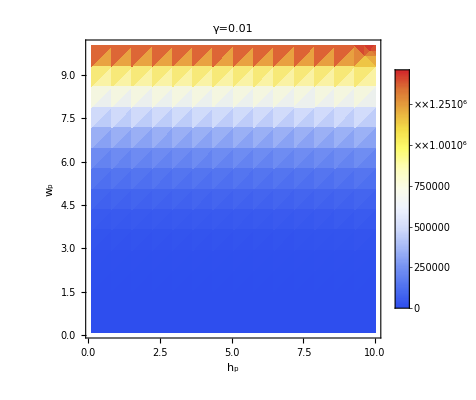
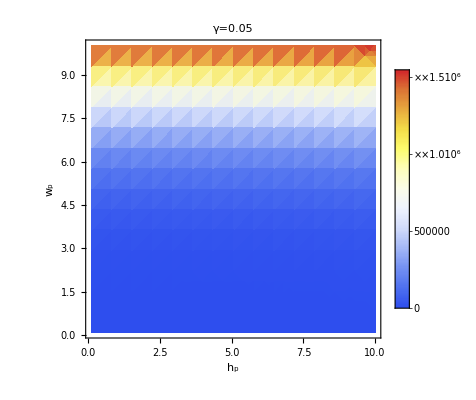
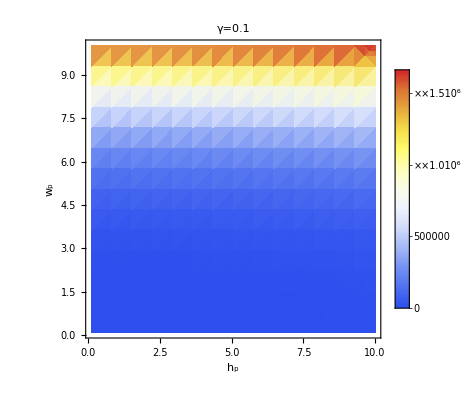
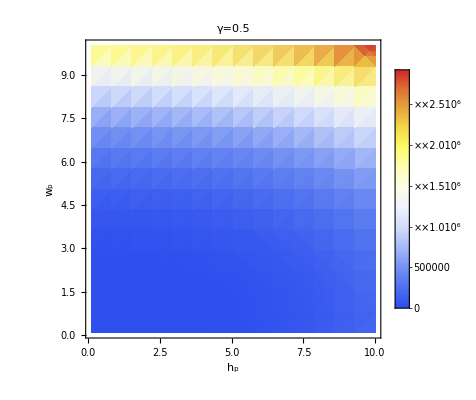
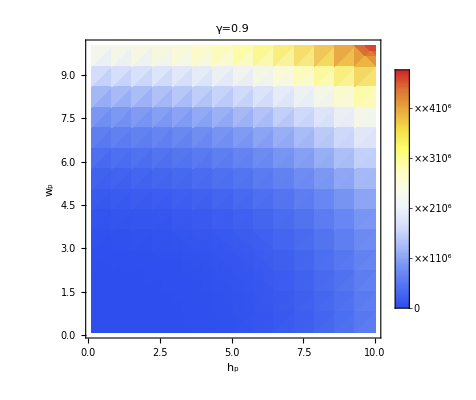

```mathematica
(*DensityPlot3D[β,{Subscript[h, p],0.1,10},{Subscript[w, p],0.1,10},{γ,0.01,0.9}] from ver10.2*)
{DensityPlot[β/.γ->0.01,{Subscript[h, p],0.1,10},{Subscript[w, p],0.1,10},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotLabel->"γ=0.01",Axes->True,AxesLabel->Automatic,AxesOrigin->{1,1}],
DensityPlot[β/.γ->0.05,{Subscript[h, p],0.1,10},{Subscript[w, p],0.1,10},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotLabel->"γ=0.05",Axes->True,AxesLabel->Automatic,AxesOrigin->{1,1}] ,
DensityPlot[β/.γ->0.1,{Subscript[h, p],0.1,10},{Subscript[w, p],0.1,10},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotLabel->"γ=0.1",Axes->True,AxesLabel->Automatic,AxesOrigin->{1,1}],DensityPlot[β/.γ->0.5,{Subscript[h, p],0.1,10},{Subscript[w, p],0.1,10},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotLabel->"γ=0.5",Axes->True,AxesLabel->Automatic,AxesOrigin->{1,1}],
DensityPlot[β/.γ->0.9,{Subscript[h, p],0.1,10},{Subscript[w, p],0.1,10},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotLabel->"γ=0.9",Axes->True,AxesLabel->Automatic,AxesOrigin->{1,1}] }
```

```mathematica
Manipulate[DensityPlot[(ω/.ωθRule)/(ω/.ωxRule)/.γ->γγ,{Subscript[h, p],0.1,10},{Subscript[w, p],0.1,10},PlotLegends->Automatic,ColorFunction->"TemperatureMap",PlotLabel->("γ= "γγ),Axes->True,AxesLabel->Automatic,AxesOrigin->{1,1},ImageSize->Small],{γγ,0.01,0.9,Appearance->"Open"},ContinuousAction->False,Deployed->True,SynchronousUpdating->False]
```

```mathematica
(*plotsss[wp_,max_,isMesh_]:={myTitle=(*"ω_i^2*)" as func of h_p & γ for constant w_p";
Plot3D[ω/.ωθRule/.{Subscript[w, p]->wp},{Subscript[h, p],0.1,max},{γ,0.01, max/10},PlotLabel->myTitle+" ω_θ",AxesLabel->{"h_p","γ"},ColorFunction->"Rainbow",Mesh->isMesh,ImageSize->Medium],
Plot3D[ω/.ωxRule/.{Subscript[w, p]->wp},{Subscript[h, p],0.1,max},{γ,0.01,max/10},PlotLabel->myTitle+"ω_x ",AxesLabel->{"h_p","γ"},ColorFunction->"Rainbow",Mesh->isMesh,ImageSize->Medium]}
Manipulate[plotsss[wp,10,True],{{wp,1},0.1,10}]*)
```

```mathematica
Manipulate[(ω/.ωθRule)/(ω/.ωxRule)/.Subscript[h, p]->hp/.Subscript[w, p]->wp/.γ->γγ,{hp,0.1,10,Appearance->"Open"},{wp,0.1,10,Appearance->"Open"},{γγ,0.01,0.9,Appearance->"Open"}]
```

## reducing order of equations from 3DOF to 2DOF